## Centroid-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 16:52:33
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

```mathematica
w=TemplateRandomSquareGrid[36, {-5,-5}, {5, 5}];
```

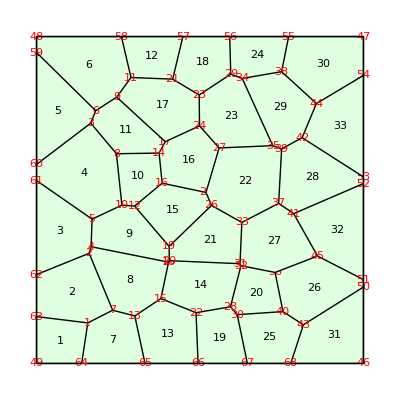

```mathematica
ShowTissue[w, "CellNumbers"-> True, "VertexNumbers"-> Red]
```

Determine the vertex numbers for cell 15

```mathematica
Centroid[w, 15]
```

{-0.824092,-0.306352}

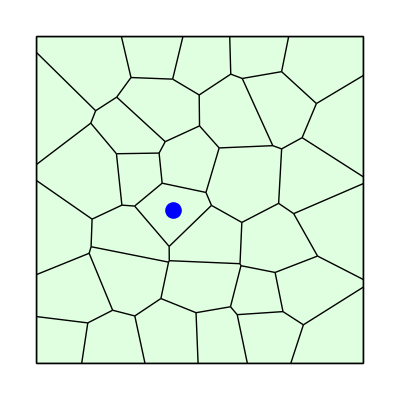

```mathematica
ShowTissue[w, Epilog-> {Blue, PointSize[.03], Point[Centroid[w,15]]}]
```

```mathematica
polygon = CellVertexCoordinates[w,15]
```

{{-1.99945,-0.185474},{-0.943473,-1.41935},{0.351073,-0.164973},{0.182578,0.23099},{-1.15785,0.514076}}

```mathematica
c=Centroid[polygon]
```

{-0.824092,-0.306352}

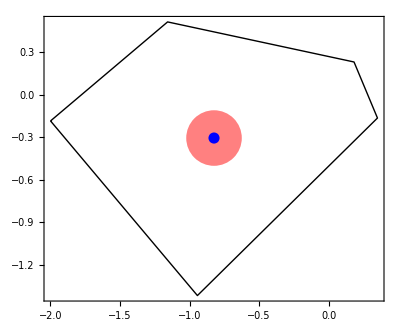

```mathematica
Show[Boundary[polygon], Graphics[{Pink, PointSize[.1], Point[c], Blue, PointSize[.02], Point[c]}], Frame-> True]
```